# Linear protocol and counterdiabatic driving in STIRAP

The boundary conditions of the reference protocol are not important and, the peaks in the reference protocols are much bigger than the boundary conditions. 
 Time-rescalling: realizar as simulações, mas lembrar que depende muito do protocolo escolhido para rescalonamento
 Santos and Sarandy. Realizei um procedimento de regularização e obtive os protocolos. Porém, esses protocolos são razoáveis? E qual a motivação teórica na literatura para regularização? 
 Questions: 1) what is the exact form of the eigenvalues of the counterdiabatic Hamiltonian? In this case, the FQ protocol is equal to the minimal time-averaged excess work protocol? 
Tarefas. Escrever resultados, formatar os gráficos, calcular os custos e investigar as questões acima.  

Work in a quantum quench? 
Minimum fidelity?

## Introduction

The STIRAP is ....

Here we calculate the population transfer, the excess work, the cost given by the Hilbert-Schmidt norm of the Hamiltonian, and the time-averaged work for different shortcuts to adiabaticity methods.

## Parameters and definitions

```mathematica
ℏ = 1
ti = 0
Δ= 0.1
(*Boundary conditions for the protocols*)
Ωpi = 0.1
Ωpf = 10
(*Range of the protocol time*)
Tmin = 0.1
Tmax = 50
(*Sample size*)
m = 9
ΔT = (Tmax-Tmin)/m
(*Protocols*)
Ωs[t_]:= 1.0
Ωp[t_, tf_]:=(Ωpf-Ωpi)*t/(tf-ti) + Ωpi
(*Counterdiabatic driving for the linear protocol*)
dΩp[t_,tf_]:=D[Ωp[b,tf],b]/.b-> t
dΩs[t_]:=D[Ωs[b],b]/.b-> t
Ωa[t_,tf_]:=2*(dΩp[t,tf]*Ωs[t]-Ωp[t,tf]*dΩs[t])/(Ωp[t,tf]^2 + Ωs[t]^2)
(*Energetic costs*)
Cost[Ωp_,Ωs_,Ωa_,Δ_,tf_] := NIntegrate[√(Δ^2 ℏ^2+(Ωa^2 ℏ^2)/2+(Ωp^2 ℏ^2)/2+(Ωs^2 ℏ^2)/2),{t,ti,tf}]/tf
Wex[c1_,c2_,c3_,Ωp_,Ωs_,Δ_] := ℏ*(Ωp*Re[c1*Conjugate[c2]] + Ωs*Re[c2*Conjugate[c3]]+ 2*Δ*Abs[c2]^2)
(*Sample points*)
time= Table[tf/2.198,{tf,Tmin,Tmax, ΔT}]
```

1

0

0.1

0.1

10

0.1

50

9

5.54444

{0.0454959,2.56799,5.09049,7.61298,10.1355,12.658,15.1805,17.703,20.2255,22.748}

## Linear protocol

The linear protocol and the variation of the eigenvalues

1.

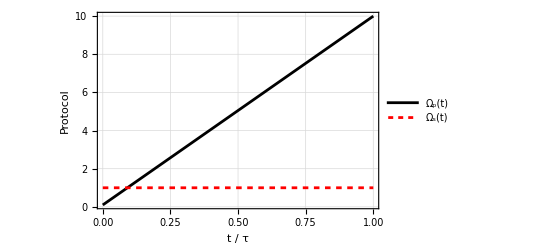

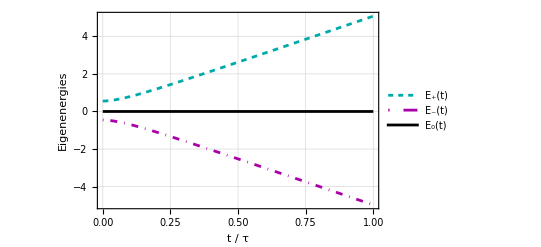

```mathematica
tf = 1.0
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
Show[Plot[0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Cyan], Dashing[0.01]},FrameLabel ->{"t / τ", "Eigenenergies"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_+(t)",10]},LegendLayout->"Row"],{Left,0.94}]],Plot[-0.5*Sqrt[Ωp[t,tf]^2 + Ωs[t]^2] + 0.5*Δ, {t,ti,tf},PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> {Darker[Magenta], DotDashed},FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_-(t)",10]},LegendLayout->"Row"],{Left,0.78}]], Plot[0,{t,ti,tf}, PlotRange->{-11,11},PlotTheme-> "Detailed",PlotStyle-> Darker[Black],FrameLabel ->{"t (μs)", "E_+(t)"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["E_0(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
```

Solution of the Schrödinger equation for the linear protocol

```mathematica
Sol = Table[NDSolve[{ⅈ*ℏ*c1'[t] ==(ℏ/2)*Ωp[t,tf]*c2[t],ⅈ*ℏ*c2'[t] ==(ℏ/2)*Ωp[t,tf]*c1[t]+(ℏ)*Δ*c2[t]+ (ℏ/2)*Ωs[t]*c3[t],ⅈ*ℏ*c3'[t] ==+(ℏ/2)*Ωs[t]*c2[t],c1[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ],c2[ti]==0,c3[ti]==-Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ] },{c1,c2,c3},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}},{{c1→InterpolatingFunction[…],c2→InterpolatingFunction[…],c3→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the excess work at the end of the protocols; the time-averaged excess work; and the cost of Santos and Sarandy for the linear protocol.

```mathematica
(*Population transfer*)
p1 = Table[Abs[c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
p2 = Table[Abs[c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
p3 = Table[Abs[c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexLIN = Table[Wex[c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3]/.t->tf,Ωp[tf,tf],Ωs[tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexLINtimeaveraged= Table[NIntegrate[Wex[c1[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],1],c2[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],2],c3[t]/.Part[Flatten[Part[Sol,(tf-Tmin)/ΔT + 1]],3],Ωp[t,tf],Ωs[t],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CLIN = Table[Cost[Ωp[t,tf],Ωs[t],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.929908,0.0375187,0.389228,0.201512,0.206037,0.223429,0.0164144,0.19164,0.0414699,0.156752}

{0.0593616,0.670766,0.102781,0.298167,0.207892,0.0691137,0.235525,0.00184238,0.16152,0.0426541}

{0.0107307,0.291713,0.50799,0.50032,0.586072,0.707458,0.748062,0.806518,0.797011,0.800594}

{0.00393292,-0.149621,-0.249904,-0.229788,-0.228878,-0.23149,-0.193596,-0.194793,-0.162147,-0.156861}

{0.000796241,-0.060364,-0.0915587,-0.101616,-0.102796,-0.0990196,-0.0931222,-0.0860926,-0.0788034,-0.0717091}

{3.69104,3.69104,3.69104,3.69104,3.69104,3.69104,3.69104,3.69104,3.69104,3.69104}

Images for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the excess work at the end of the protocols; the time-averaged excess work; and the cost of Santos and Sarandy for the linear protocol.

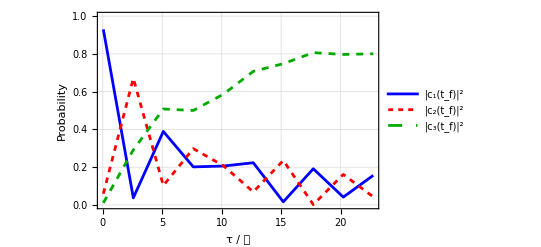

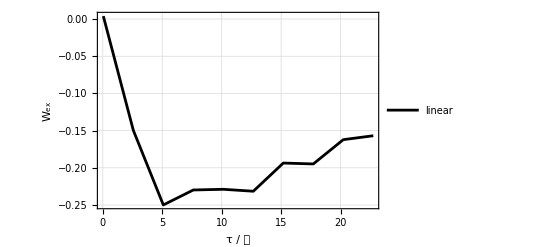

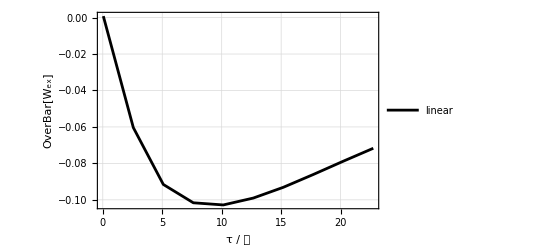

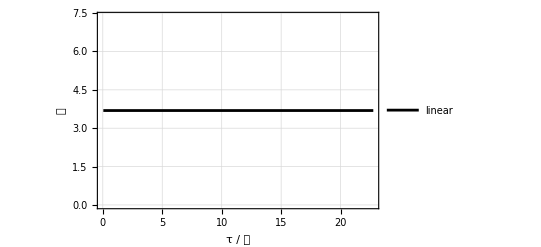

```mathematica
(*Population transfer*)
gLIN = Show[ListPlot[Transpose[{time,p1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{0.2,0.94}]],ListPlot[Transpose[{time,p2}], PlotStyle->{Red, Dashing[0.01]}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{0.2,0.86}]],ListPlot[Transpose[{time,p3}], PlotStyle->{Darker[Green], Dashed}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{0.2,0.78}]]]
(*Excess work*)
gWexLIN =ListPlot[Transpose[{time,WexLIN}], Joined->True,PlotStyle->{Black}, PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "W_ex"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["linear",10]},LegendLayout->"Row"],{Right,0.94}]]
(*Time-averaged excess work*)
gWexLINtimeaveraged =ListPlot[Transpose[{time,WexLINtimeaveraged}], Joined->True,PlotStyle->{Black}, PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "OverBar[W_ex]"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["linear",10]},LegendLayout->"Row"],{Right,0.94}]]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
gCLIN = ListPlot[Transpose[{time,CLIN}], Joined->True,PlotStyle->{Black}, PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["linear",10]},LegendLayout->"Row"],{Right,0.94}]]
```

## Counterdiabatic driving

The protocols applied during counterdiabatic driving.

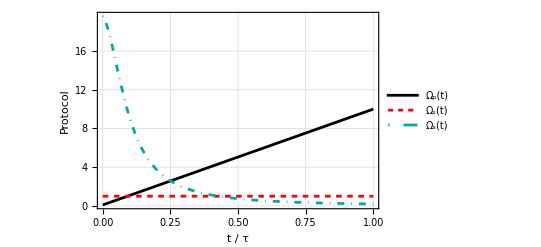

```mathematica
Show[Plot[Ωp[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Right,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.86}]], Plot[Ωa[s*tf,tf],{s,ti/tf,tf/tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Darker[Cyan], DotDashed},FrameLabel ->{"t / τ", "Ω_a"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.78}]]
]
```

Solution of the Schrödinger equation for the linear protocol under counterdiabatic driving

```mathematica
SolCD = Table[NDSolve[{ⅈ*ℏ*c1CD'[t] ==(ℏ/2)*Ωp[t,tf]*c2CD[t]+ⅈ*(ℏ/2)*Ωa[t,tf]*c3CD[t],ⅈ*ℏ*c2CD'[t] ==(ℏ/2)*Ωp[t,tf]*c1CD[t]+(ℏ)*Δ*c2CD[t]+(ℏ/2)*Ωs[t]*c3CD[t],ⅈ*ℏ*c3CD'[t] ==-ⅈ*(ℏ/2)*Ωa[t,tf]*c1CD[t]+(ℏ/2)*Ωs[t]*c2CD[t],c1CD[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ],c2CD[ti]==0,c3CD[ti]==-Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ] },{c1CD,c2CD,c3CD},{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}},{{c1CD→InterpolatingFunction[…],c2CD→InterpolatingFunction[…],c3CD→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the linear protocol under counterdiabatic driving. Note that the excess work at the end of the protocol is close () to zero.

```mathematica
(*Population transfer*)
pCD1 = Table[Abs[c1CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pCD2 = Table[Abs[c2CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pCD3 = Table[Abs[c3CD[t]/.Part[Flatten[Part[SolCD,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)WexCDtimeaveraged[Ωp_,Ωs_,Ωa_,Δ_,tf_]:= -NIntegrate[2*Δ/3*(1+(2*Ωa^2/(Ωp^2 + Ωs^2) - 1)/(Ωa^2/(Ωp^2 + Ωs^2) + 1)),{t,ti,tf}]/tf
listWexCDtimeaveraged = Table[WexCDtimeaveraged[Ωp[t,tf],Ωs[t],Ωa[t,tf],Δ,tf],{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CCD = Table[Cost[Ωp[t,tf],Ωs[t],Ωa[t,tf],Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.00990098,0.00990099,0.00990098,0.00990099,0.00990099,0.009901,0.00990098,0.00990099,0.00990099,0.00990099}

{6.91135×10^-18,3.21726×10^-15,2.2214×10^-15,4.25272×10^-15,4.88919×10^-15,6.19054×10^-16,9.73164×10^-17,9.17548×10^-16,2.35108×10^-16,1.52507×10^-16}

{0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099,0.990099}

{-0.117924,-0.0217611,-0.012596,-0.00806546,-0.00548577,-0.00391585,-0.00290926,-0.00223411,-0.00176327,-0.00142375}

{21.2558,3.83455,3.74014,3.71554,3.7056,3.70064,3.69783,3.69609,3.69494,3.69414}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the linear protocol under counterdiabatic driving.

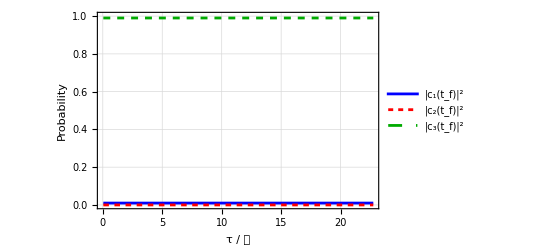

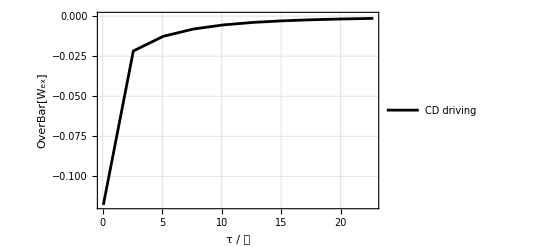

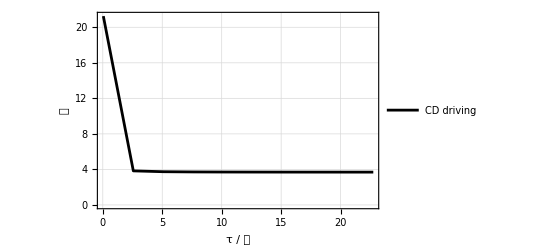

```mathematica
(*Population transfer*)
gCD = Show[ListPlot[Transpose[{time,pCD1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pCD2}], PlotStyle->{Red, Dashing[0.01]}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pCD3}], PlotStyle->{Darker[Green], Dashed}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
(*Time-averaged excess work*)
 gWexCDtimeaveraged = ListPlot[Transpose[{time,listWexCDtimeaveraged}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "OverBar[W_ex]"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["CD driving",10]},LegendLayout->"Row"],{Right,0.94}]]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
gCCD = ListPlot[Transpose[{time,CCD}], Joined->True, PlotStyle-> Black,PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["CD driving",10]},LegendLayout->"Row"],{Right,0.94}]]
```

## Physical unitary transformation

Protocols for the physical unitary transformation. Due to boundary conditions of this STA method, the protocol of reference   used is the same as the boundary cancellation method (BCM).

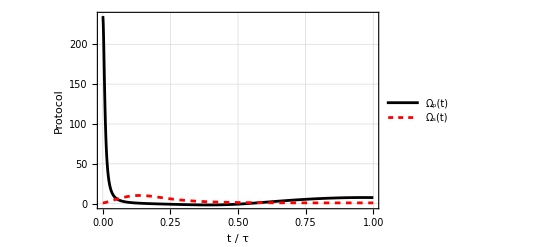

```mathematica
ΩpBCM[t_,tf_]:= Ωpi + ( Ωpf- Ωpi)*(3*((t-ti)/(tf-ti))^2 - 2*((t-ti)/(tf-ti))^3)
dΩpBCM[t_,tf_]:=D[ΩpBCM[b,tf],b]/.b-> t
ΩaBCM[t_,tf_]:=2*(dΩpBCM[t,tf]*Ωs[t]-ΩpBCM[t,tf]*dΩs[t])/(ΩpBCM[t,tf]^2 + Ωs[t]^2)
α[t_,tf_]:=  ArcTan[-ΩaBCM[t,tf]/(Ωs[t])]
ΩpUT[t_,tf_]:=ΩpBCM[t,tf] -(2/ℏ)*D[α[x,tf],x]/.x->t
ΩsUT[t_,tf_]:=Ωs[t]*Cos[α[t,tf]] - ΩaBCM[t,tf]*Sin[α[t,tf]]/ℏ
Show[Plot[ΩpUT[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Right,0.94}]],
Plot[ΩsUT[t,tf],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Right,0.86}]]
]
```

Solution of the Schrödinger equation for a system under the physical unitary transformation method.

```mathematica
SolUT = Table[NDSolve[{ⅈ*ℏ*c1UT'[t] ==(ℏ/2)*ΩpUT[t,tf]*c2UT[t],ⅈ*ℏ*c2UT'[t] ==(ℏ/2)*ΩpUT[t,tf]*c1UT[t]+(ℏ)*Δ*c2UT[t]+ (ℏ/2)*ΩsUT[t,tf]*c3UT[t],ⅈ*ℏ*c3UT'[t] ==+(ℏ/2)*ΩsUT[t,tf]*c2UT[t],c1UT[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ],c2UT[ti]==0,c3UT[ti]==-Ωp[ti,tf]/Sqrt[Ωs[ti]^2 + Ωp[ti,tf]^2 ] },{c1UT,c2UT,c3UT},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}},{{c1UT→InterpolatingFunction[…],c2UT→InterpolatingFunction[…],c3UT→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the unitary transformation method.

```mathematica
(*Population transfer*)
pUT1 = Table[Abs[c1UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pUT2 = Table[Abs[c2UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pUT3 = Table[Abs[c3UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexUT = Table[Wex[c1UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],3]/.t->tf,ΩpUT[tf,tf],ΩsUT[tf,tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexUTtimeaveraged= Table[NIntegrate[Wex[c1UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],1],c2UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],2],c3UT[t]/.Part[Flatten[Part[SolUT,(tf-Tmin)/ΔT + 1]],3],ΩpUT[t,tf],ΩsUT[t,tf],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CUT = Table[Cost[ΩpUT[t,tf],ΩsUT[t,tf],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.00990306,0.0153831,0.0106537,0.00620521,0.0169458,0.0214176,0.00273079,0.00736227,0.0180419,0.00912142}

{4.9765×10^-7,0.000848868,0.00744143,0.000340539,0.0047478,0.00199246,0.000925445,0.00199139,0.0000177969,0.000848385}

{0.990096,0.983768,0.981905,0.993454,0.978306,0.97659,0.996344,0.990646,0.98194,0.99003}

{0.0165134,0.00217295,0.00290079,0.000817,-0.000161246,-0.00129509,-0.00172172,-0.0016,-0.00159459,-0.00123282}

{0.0627527,0.0251741,0.0081945,0.00200972,-0.000279979,-0.00110096,-0.00130361,-0.00123985,-0.00106634,-0.000862618}

{58.1508,3.84597,3.7429,3.72883,3.72737,3.72795,3.72872,3.72936,3.72985,3.73023}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the unitary transformation method.

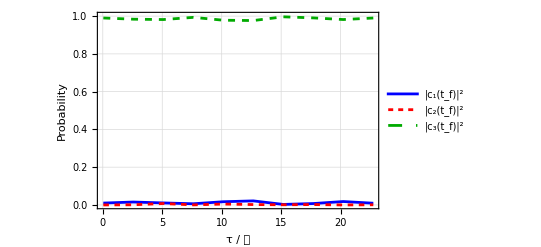

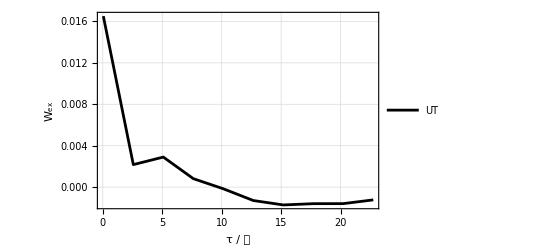

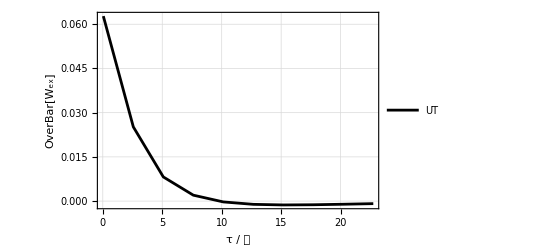

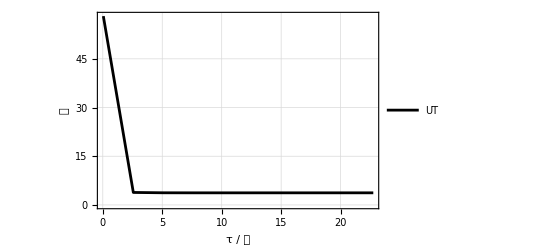

```mathematica
gUT = Show[ListPlot[Transpose[{time,pUT1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pUT2}], PlotStyle->{Red, Dashing[0.01]}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pUT3}], PlotStyle->{Darker[Green], Dashed}, Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
(*Excess work*)
 gWexUT = ListPlot[Transpose[{time,WexUT}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "W_ex"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["UT",10]},LegendLayout->"Row"],{Right,0.94}]]
(*Time-averaged excess work*)
 gWexUTtimeaveraged = ListPlot[Transpose[{time,WexUTtimeaveraged}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "OverBar[W_ex]"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["UT",10]},LegendLayout->"Row"],{Right,0.94}]]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
gCUT = ListPlot[Transpose[{time,CUT}], Joined->True, PlotStyle-> Black,PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["UT",10]},LegendLayout->"Row"],{Right,0.94}]]
```

## Reference protocol

```mathematica
Ω0 = 42506.6114781728
Ωpref[t_,tf_]:= Ω0*Exp[-(t-tf/2-tf/10)^2/(tf/6)^2]
Ωsref[t_,tf_]:= Ω0*Exp[-(t-tf/2+tf/10)^2/(tf/6)^2]
```

42506.6

## Minimal action

The protocols of the minimal action (MA) method comes from the minimization of the adiabatic action.

```mathematica
ProtMA = Table[NDSolve[{D[ΩpMA'[t]/(ΩpMA[t]^2 + Ωs[t]^2),t] + 4*Δ/(ΩpMA[t]^2 + Ωs[t]^2)^(3/2)*(ΩpMA''[t] - 2.5*ΩpMA[t]*ΩpMA'[t]^2/(ΩpMA[t]^2 + Ωs[t]^2)) ==0 , ΩpMA[ti]==Ωpi, ΩpMA[tf]==Ωpf},ΩpMA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}},{{ΩpMA→InterpolatingFunction[…]}}}

1

0.1

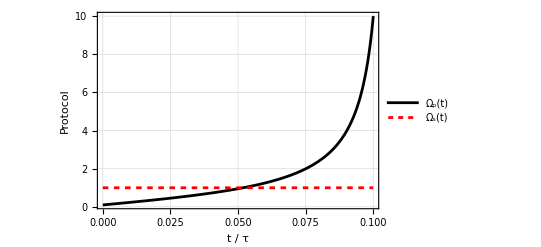

```mathematica
(*Protocol time for the Figure*)
n = 1
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]
]
```

Solution of the Schrödinger equation for a system under the physical unitary transformation method.

```mathematica
SolMA = Table[NDSolve[{ⅈ*ℏ*c1MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c2MA[t],ⅈ*ℏ*c2MA'[t] ==(ℏ/2)*Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]*c1MA[t]+(ℏ)*Δ*c2MA[t]+ (ℏ/2)*Ωs[t]*c3MA[t],ⅈ*ℏ*c3MA'[t] ==+(ℏ/2)*Ωs[t]*c2MA[t],c1MA[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2MA[ti]==0,c3MA[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1MA,c2MA,c3MA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}},{{c1MA→InterpolatingFunction[…],c2MA→InterpolatingFunction[…],c3MA→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the minimal action protocol.

```mathematica
(*Population transfer*)
pMA1 = Table[Abs[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA2 = Table[Abs[c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pMA3 = Table[Abs[c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexMA = Table[Wex[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3]/.t->tf,Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]]/.t->tf,Ωs[tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexMAtimeaveraged= Table[NIntegrate[Wex[c1MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],1],c2MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],2],c3MA[t]/.Part[Flatten[Part[SolMA,(tf-Tmin)/ΔT + 1]],3],Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]],Ωs[t],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CMA = Table[Cost[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,(tf-Tmin)/ΔT + 1]]],Ωs[t],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.984324,0.00268822,0.0129772,0.0129414,0.0119442,0.0121853,0.0121445,0.0100712,0.00652405,0.00420834}

{0.0056101,0.200304,0.0163458,0.00139813,0.00601259,0.00833372,0.0057602,0.00185471,0.0000365165,0.000717096}

{0.0100656,0.797008,0.970677,0.98566,0.982043,0.979481,0.982095,0.988074,0.993439,0.995074}

{-0.000498798,-0.26424,-0.109414,-0.0568212,-0.0307903,-0.0148949,-0.00603933,-0.00235867,-0.00177085,-0.00236481}

{-6.51827×10^-6,-0.0291714,-0.0121943,-0.00514598,-0.00277181,-0.0017463,-0.00121879,-0.000908907,-0.000705625,-0.00056105}

{1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548,1.45548}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the minimal action protocol.

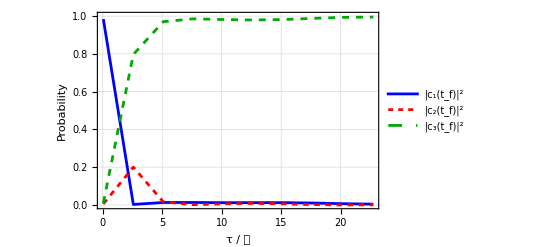

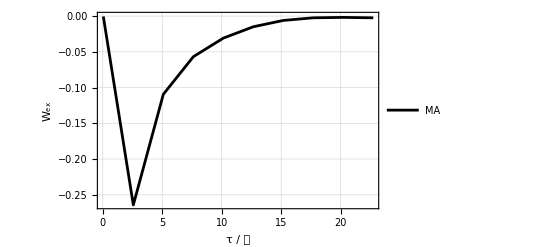

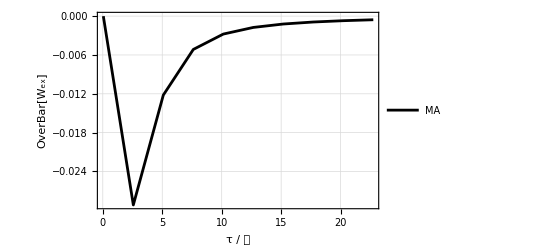

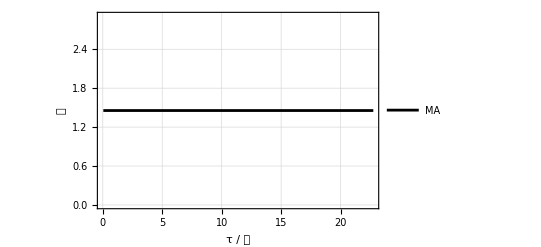

```mathematica
gMA = Show[ListPlot[Transpose[{time,pMA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pMA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pMA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
(*Excess work*)
 gWexMA = ListPlot[Transpose[{time,WexMA}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "W_ex"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time-averaged excess work*)
 gWexMAtimeaveraged = ListPlot[Transpose[{time,WexMAtimeaveraged}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "OverBar[W_ex]"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
gCMA = ListPlot[Transpose[{time,CMA}], Joined->True, PlotStyle-> Black,PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["MA",10]},LegendLayout->"Row"],{Right,0.94}]]
```

## Fast quasidiabatic

The protocols for the fast quasidiabatic method (FQ) can be found by solving the EDO generated when we make the adiabatic quantitative condition constant.

```mathematica
ProtFQ = Table[NDSolve[{D[ΩpFQ'[t]/(ΩpFQ[t]^2 + Ωs[t]^2)^(3/2)*(1+1.5*Δ/(ΩpFQ[t]^2 + Ωs[t]^2)^(1/2)),t] ==0 , ΩpFQ[ti]==Ωpi, ΩpFQ[tf]==Ωpf},ΩpFQ,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}},{{ΩpFQ→InterpolatingFunction[…]}}}

Protocols for the fast quasidiabatic method.

1

0.1

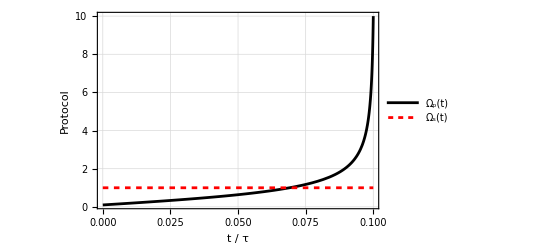

```mathematica
(*Protocol time for the Figure*)
n = 1
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t)",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.86}]]]
```

Solution of the Schrödinger equation for the fast quasidiabatic protocol.

```mathematica
SolFQ = Table[NDSolve[{ⅈ*ℏ*c1FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c2FQ[t],ⅈ*ℏ*c2FQ'[t] ==(ℏ/2)*Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]*c1FQ[t]+(ℏ)*Δ*c2FQ[t]+ (ℏ/2)*Ωs[t]*c3FQ[t],ⅈ*ℏ*c3FQ'[t] ==+(ℏ/2)*Ωs[t]*c2FQ[t],c1FQ[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2FQ[ti]==0,c3FQ[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1FQ,c2FQ,c3FQ},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}},{{c1FQ→InterpolatingFunction[…],c2FQ→InterpolatingFunction[…],c3FQ→InterpolatingFunction[…]}}}

Data for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the fast quasidiabatic protocol.

```mathematica
(*Population transfer*)
pFQ1 = Table[Abs[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ2 = Table[Abs[c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pFQ3 = Table[Abs[c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
(*Excess work*)
WexFQ = Table[Wex[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1]/.t->tf,c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2]/.t->tf,c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3]/.t->tf,Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]]/.t->tf,Ωs[tf],Δ],{tf,Tmin,Tmax,ΔT}]
(*Time-averaged excess work*)
WexFQtimeaveraged= Table[NIntegrate[Wex[c1FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],1],c2FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],2],c3FQ[t]/.Part[Flatten[Part[SolFQ,(tf-Tmin)/ΔT + 1]],3],Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]],Ωs[t],Δ],{t,ti,tf}]/tf,{tf,Tmin,Tmax,ΔT}]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
CFQ = Table[Cost[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,(tf-Tmin)/ΔT + 1]]],Ωs[t],0,Δ,tf],{tf,Tmin,Tmax,ΔT}]
```

{0.988126,0.0359962,0.0447439,0.0106516,0.00961527,0.0153444,0.00834906,0.0151417,0.00773029,0.00860836}

{0.00187438,0.146895,0.0654347,0.00742654,0.0125174,0.00648906,0.00659016,0.00280291,0.000953244,0.00489469}

{0.00999996,0.817108,0.889821,0.981922,0.977867,0.978166,0.985061,0.982055,0.991316,0.986497}

{-0.000602043,-0.3779,0.0504174,0.0117853,-0.0678195,0.0281024,0.000198183,-0.0220817,0.00970121,-0.00200368}

{-3.36497×10^-6,-0.0122677,-0.000760596,-0.00230784,-0.000591812,-0.000279874,-0.000517296,-0.000201298,-0.000156836,-0.000183686}

{1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191,1.07191}

Figures for the population transfer from the state  to   at the end of the protocol for protocols of different durations; the time-averaged excess work; and the cost of Santos and Sarandy for the fast quasidiabatic protocol.

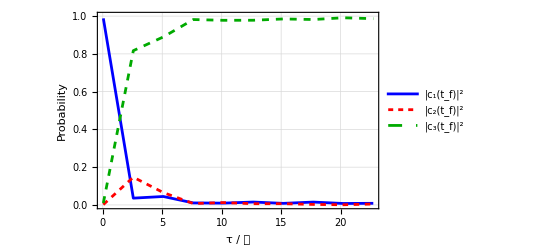

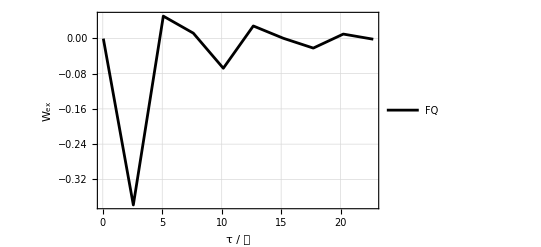

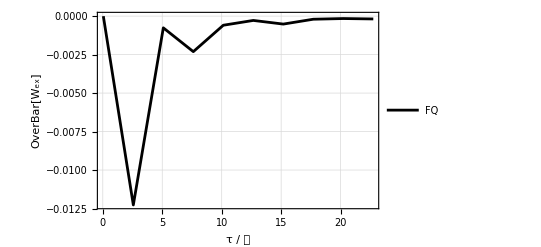

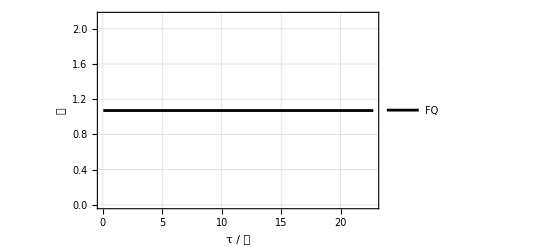

```mathematica
(*Population transfer*)
gFQ = Show[ListPlot[Transpose[{time,pFQ1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.94}]],ListPlot[Transpose[{time,pFQ2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.86}]],ListPlot[Transpose[{time,pFQ3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.78}]]]
(*Excess work*)
 gWexFQ = ListPlot[Transpose[{time,WexFQ}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "W_ex"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time-averaged excess work*)
 gWexFQtimeaveraged = ListPlot[Transpose[{time,WexFQtimeaveraged}], Joined->True, PlotRange->All,PlotStyle->Black,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "OverBar[W_ex]"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.10}]]
(*Time average of the Hamiltonian's Hilbert-Schmidt norm*)
gCFQ = ListPlot[Transpose[{time,CFQ}], Joined->True, PlotStyle-> Black,PlotRange->All,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "𝒞"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["FQ",10]},LegendLayout->"Row"],{Right,0.94}]]
```

## Boundary cancellation method

```mathematica
ΩpBCM[t_,tf_]:= Ωpi + ( Ωpf- Ωpi)*(3*((t-ti)/(tf-ti))^2 - 2*((t-ti)/(tf-ti))^3)
```

```mathematica
SolBCM = Table[NDSolve[{ⅈ*ℏ*c1BCM'[t] ==(ℏ/2)*ΩpBCM[t,tf]*c2BCM[t],ⅈ*ℏ*c2BCM'[t] ==(ℏ/2)*ΩpBCM[t,tf]*c1BCM[t]+(ℏ)*Δ*c2BCM[t]+ (ℏ/2)*Ωs[t]*c3BCM[t],ⅈ*ℏ*c3BCM'[t] ==+(ℏ/2)*Ωs[t]*c2BCM[t],c1BCM[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2BCM[ti]==0,c3BCM[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1BCM,c2BCM,c3BCM},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}},{{c1BCM→InterpolatingFunction[…],c2BCM→InterpolatingFunction[…],c3BCM→InterpolatingFunction[…]}}}

```mathematica
pBCM1 = Table[Abs[c1BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pBCM2 = Table[Abs[c2BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pBCM3 = Table[Abs[c3BCM[t]/.Part[Flatten[Part[SolBCM,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.929984,0.0167789,0.3952,0.0888624,0.223011,0.0779105,0.0277839,0.0594508,0.0198989,0.0521319}

{0.0593703,0.698334,0.0406459,0.30336,0.074599,0.0819636,0.0763144,0.00778326,0.0423347,0.00396832}

{0.0106462,0.284887,0.564155,0.607778,0.702391,0.840126,0.895902,0.932766,0.937767,0.9439}

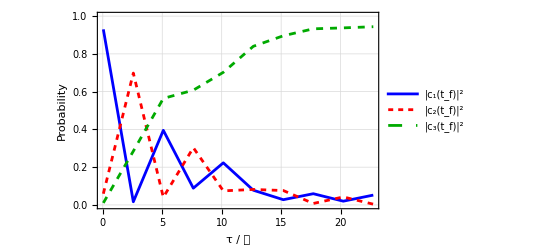

```mathematica
gBCM = Show[ListPlot[Transpose[{time,pBCM1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pBCM2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pBCM3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Optimal time-averaged excess work

Apparently, the protocol found by optimizing the time-averaged excess work is equal to de fast quasidiabatic protocol. The protocols can be found by using the Euler-Lagrange equations on the excess work. The solutions are given below.

```mathematica
ProtOP = Table[NDSolve[{(1+ΩpOP[t]^2) (1+3 ΩpOP[t]^2+3 ΩpOP[t]^4+ΩpOP[t]^6-12 ΩpOP'[t]^2) (-3 ΩpOP[t] ΩpOP'[t]^2+ΩpOP''[t]+ΩpOP[t]^2 ΩpOP''[t])==0, ΩpOP[ti]==Ωpi, ΩpOP[tf]==Ωpf},ΩpOP[t],{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}},{{ΩpOP[t]→InterpolatingFunction[…][t]}}}

Protocol found by minimizing the time-averaged excess work.

1

0.1

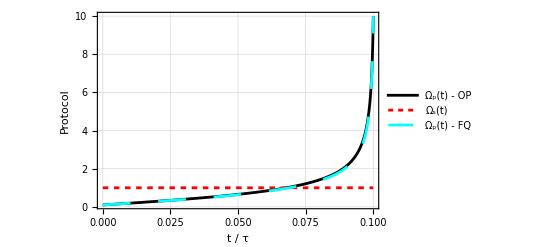

```mathematica
(*Protocol time for the Figure*)
n = 1
tf = Tmin + (n-1)*ΔT
Show[Plot[Evaluate[ΩpOP[t]/.Flatten[Part[ProtOP, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Black},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - OP",10]},LegendLayout->"Row"],{Left,0.94}]],
Plot[Ωs[t],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Red, Dashing[0.01]},FrameLabel ->{"t / τ", "Ω_s"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_s(t)",10]},LegendLayout->"Row"],{Left,0.78}]], Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ, n]]],{t,ti,tf},PlotRange->All,PlotTheme-> "Detailed",PlotStyle-> {Cyan, Dashing[0.05]},FrameLabel ->{"t / τ", "Protocol"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["Ω_p(t) - FQ",10]},LegendLayout->"Row"],{Left,0.86}]]
]
```

## Optimal Zheng-2 energetic cost

```mathematica
ProtZh=Table[NDSolve[{ΩpZh''[t]==(2 ΩpZh[t] ΩpZh'[t]^2)/(1+ΩpZh[t]^2), ΩpZh[ti]==Ωpi, ΩpZh[tf]==Ωpf},ΩpZh[t],{t,ti,tf}], {tf,Tmin,Tmax,ΔT}]
```

{{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}},{{ΩpZh[t]→InterpolatingFunction[…][t]}}}

```mathematica
SolZh = Table[NDSolve[{ⅈ*ℏ*c1Zh'[t] ==(ℏ/2)*Evaluate[ΩpZh[t]/.Flatten[Part[ProtZh,(tf-Tmin)/ΔT + 1]]]*c2Zh[t],ⅈ*ℏ*c2Zh'[t] ==(ℏ/2)*Evaluate[ΩpZh[t]/.Flatten[Part[ProtZh,(tf-Tmin)/ΔT + 1]]]*c1Zh[t]+(ℏ)*Δ*c2Zh[t]+ (ℏ/2)*Ωs[t]*c3Zh[t],ⅈ*ℏ*c3Zh'[t] ==+(ℏ/2)*Ωs[t]*c2Zh[t],c1Zh[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2Zh[ti]==0,c3Zh[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1Zh,c2Zh,c3Zh},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}},{{c1Zh→InterpolatingFunction[…],c2Zh→InterpolatingFunction[…],c3Zh→InterpolatingFunction[…]}}}

```mathematica
pZh1 = Table[Abs[c1Zh[t]/.Part[Flatten[Part[SolZh,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pZh2 = Table[Abs[c2Zh[t]/.Part[Flatten[Part[SolZh,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pZh3 = Table[Abs[c3Zh[t]/.Part[Flatten[Part[SolZh,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.983769,0.0155526,0.00328658,0.00904342,0.0132901,0.0156822,0.0159536,0.0142202,0.0110871,0.00753172}

{0.00615583,0.220416,0.0389213,0.00637992,0.000849764,0.00179627,0.00352124,0.00412613,0.00341974,0.00202752}

{0.0100749,0.764032,0.957792,0.984577,0.98586,0.982521,0.980525,0.981653,0.985493,0.99044}

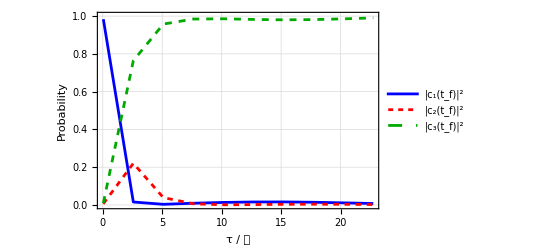

```mathematica
gZh = Show[ListPlot[Transpose[{time,pZh1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pZh2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pZh3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Uniform adiabatic

```mathematica
f[x_,a_,d_]:= Log[√(a^2+x^2)]/(2 d)-Log[2 d^2+d √(a^2+x^2)]/(2 d)
```

```mathematica
c[tf_] := 2*(f[Ωpf,Ωs[ti],Δ] -  f[Ωpi,Ωs[ti],Δ])/tf
```

```mathematica
(*ProtUA = Table[NDSolve[{D[ΩpUA[t]*ΩpUA'[t]/((ΩpUA[t]^2 + Ωs[t]^2)*((ΩpUA[t]^2 + Ωs[t]^2)^(1/2)- 2*Δ)),t] ==0 , ΩpUA[ti]==Ωpi, ΩpUA[tf]==Ωpf},ΩpUA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]*)
ProtUA = Table[NDSolve[{ΩpUA[t]*ΩpUA'[t]/((ΩpUA[t]^2 + Ωs[t]^2)*((ΩpUA[t]^2 + Ωs[t]^2)^(1/2)+ 2*Δ))==c[tf]/2 , ΩpUA[ti]==Ωpi},ΩpUA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}},{{ΩpUA→InterpolatingFunction[…]}}}

```mathematica
SolUA = Table[NDSolve[{ⅈ*ℏ*c1UA'[t] ==(ℏ/2)*Evaluate[ΩpUA[t]/.Flatten[Part[ProtUA,(tf-Tmin)/ΔT + 1]]]*c2UA[t],ⅈ*ℏ*c2UA'[t] ==(ℏ/2)*Evaluate[ΩpUA[t]/.Flatten[Part[ProtUA,(tf-Tmin)/ΔT + 1]]]*c1UA[t]+(ℏ)*Δ*c2UA[t]+ (ℏ/2)*Ωs[t]*c3UA[t],ⅈ*ℏ*c3UA'[t] ==+(ℏ/2)*Ωs[t]*c2UA[t],c1UA[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2UA[ti]==0,c3UA[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1UA,c2UA,c3UA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}},{{c1UA→InterpolatingFunction[…],c2UA→InterpolatingFunction[…],c3UA→InterpolatingFunction[…]}}}

```mathematica
pUA1 = Table[Abs[c1UA[t]/.Part[Flatten[Part[SolUA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pUA2 = Table[Abs[c2UA[t]/.Part[Flatten[Part[SolUA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pUA3 = Table[Abs[c3UA[t]/.Part[Flatten[Part[SolUA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.977656,0.331618,0.0193874,0.051589,0.0585938,0.00496364,0.0354925,0.0385245,0.0104823,0.0509935}

{0.0121521,0.110217,0.192333,0.0485519,0.0115242,0.0656442,0.0238961,0.00480931,0.0366542,0.0146192}

{0.0101919,0.558166,0.788279,0.899858,0.929881,0.929392,0.940611,0.956666,0.952863,0.934387}

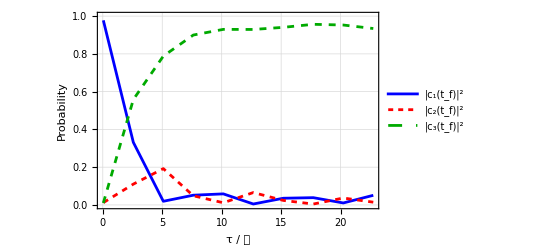

```mathematica
gUA = Show[ListPlot[Transpose[{time,pUA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pUA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pUA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Local adiabatic

```mathematica
ProtLA = Table[NDSolve[{D[ΩpLA'[t]/((ΩpLA[t]^2 + Ωs[t]^2)*(1+ 2*Δ/(ΩpLA[t]^2 + Ωs[t]^2)^(1/2))),t] ==0 , ΩpLA[ti]==Ωpi, ΩpLA[tf]==Ωpf},ΩpLA,{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

{{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}},{{ΩpLA→InterpolatingFunction[…]}}}

```mathematica
SolLA = Table[NDSolve[{ⅈ*ℏ*c1LA'[t] ==(ℏ/2)*Evaluate[ΩpLA[t]/.Flatten[Part[ProtLA,(tf-Tmin)/ΔT + 1]]]*c2LA[t],ⅈ*ℏ*c2LA'[t] ==(ℏ/2)*Evaluate[ΩpLA[t]/.Flatten[Part[ProtLA,(tf-Tmin)/ΔT + 1]]]*c1LA[t]+(ℏ)*Δ*c2LA[t]+ (ℏ/2)*Ωs[t]*c3LA[t],ⅈ*ℏ*c3LA'[t] ==+(ℏ/2)*Ωs[t]*c2LA[t],c1LA[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2LA[ti]==0,c3LA[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1LA,c2LA,c3LA},{t,ti,tf}],{tf,Tmin, Tmax, ΔT}]
```

{{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}},{{c1LA→InterpolatingFunction[…],c2LA→InterpolatingFunction[…],c3LA→InterpolatingFunction[…]}}}

```mathematica
pLA1 = Table[Abs[c1LA[t]/.Part[Flatten[Part[SolLA,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pLA2 = Table[Abs[c2LA[t]/.Part[Flatten[Part[SolLA,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
pLA3 = Table[Abs[c3LA[t]/.Part[Flatten[Part[SolLA,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax,ΔT}]
```

{0.983106,0.0623259,0.00162178,0.00191454,0.00648966,0.0117105,0.0164513,0.0199981,0.0219284,0.0221301}

{0.00680799,0.213653,0.0638327,0.0234471,0.009881,0.00418875,0.00161151,0.000517975,0.000193651,0.000264391}

{0.010086,0.724022,0.934546,0.974638,0.983629,0.9841,0.981937,0.979484,0.977878,0.977605}

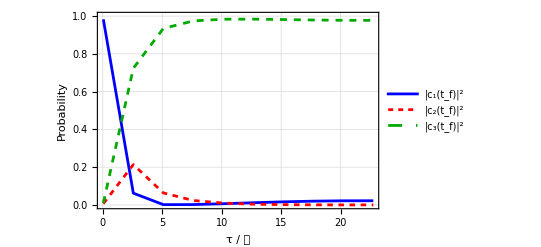

```mathematica
gLA = Show[ListPlot[Transpose[{time,pLA1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pLA2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pLA3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

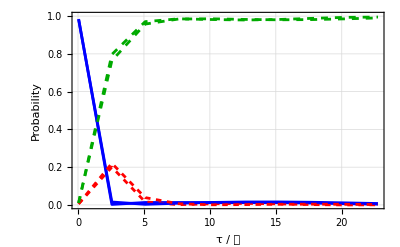

```mathematica
Show[gMA, gZh]
```

## Optimal Santos/Sarandy

```mathematica
Ωmax = 0.1
ProtSa =Table[ NDSolve[{(ΩpSa[t] ((1+ΩpSa[t]^2/(1+ΩpSa[t]^2/Ωmax^2))^3+8 (ΩpSa'[t])^2))/(√(1+ΩpSa[t]^2/Ωmax^2) (1+ΩpSa[t]^2/(1+ΩpSa[t]^2/Ωmax^2)))==4*ΩpSa''[t], ΩpSa[ti]==Ωpi, ΩpSa[tf]==Ωpf},ΩpSa[t],{t,ti,tf}],{tf,Tmin,Tmax,ΔT}]
```

0.1

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: The scaled boundary value residual error of 4.55149×10^6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::berr: The scaled boundary value residual error of 7.77811×10^6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

NDSolve::berr: The scaled boundary value residual error of 8.92799×10^6 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr will be suppressed during this calculation.

{{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}},{{ΩpSa[t]→InterpolatingFunction[…][t]}}}

```mathematica
SolSa = Table[NDSolve[{ⅈ*ℏ*c1Sa'[t] ==(ℏ/2)*Evaluate[ΩpSa[t]/.Flatten[Part[ProtSa,(tf-Tmin)/ΔT + 1]]]*c2Sa[t],ⅈ*ℏ*c2Sa'[t] ==(ℏ/2)*Evaluate[ΩpSa[t]/.Flatten[Part[ProtSa,(tf-Tmin)/ΔT + 1]]]*c1Sa[t]+(ℏ)*Δ*c2Sa[t]+ (ℏ/2)*Ωs[t]*c3Sa[t],ⅈ*ℏ*c3Sa'[t] ==+(ℏ/2)*Ωs[t]*c2Sa[t],c1Sa[ti]==Ωs[ti]/Sqrt[Ωs[ti]^2 + Ωpi^2 ],c2Sa[ti]==0,c3Sa[ti]==-Ωpi/Sqrt[Ωs[ti]^2 + Ωpi^2 ] },{c1Sa,c2Sa,c3Sa},{t,ti,tf}],{tf,Tmin, Tmax-0*ΔT, ΔT}]
```

{{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}},{{c1Sa→InterpolatingFunction[…],c2Sa→InterpolatingFunction[…],c3Sa→InterpolatingFunction[…]}}}

```mathematica
pSa1 = Table[Abs[c1Sa[t]/.Part[Flatten[Part[SolSa,(tf-Tmin)/ΔT + 1]],1]]^2/.t->tf,{tf,Tmin,Tmax-0*ΔT,ΔT}]
pSa2 = Table[Abs[c2Sa[t]/.Part[Flatten[Part[SolSa,(tf-Tmin)/ΔT + 1]],2]]^2/.t->tf,{tf,Tmin,Tmax-0*ΔT,ΔT}]
pSa3 = Table[Abs[c3Sa[t]/.Part[Flatten[Part[SolSa,(tf-Tmin)/ΔT + 1]],3]]^2/.t->tf,{tf,Tmin,Tmax-0*ΔT,ΔT}]
```

{0.960804,0.352541,0.374564,0.137471,0.0303707,0.0290611,0.0449827,0.0461217,0.0308661,0.0696448}

{0.0288037,0.130796,0.0100252,0.00920762,0.0318278,0.0100452,0.0280696,0.0131685,0.0183531,0.0183786}

{0.0103923,0.516663,0.61541,0.853321,0.937801,0.960893,0.926947,0.94071,0.950781,0.911976}

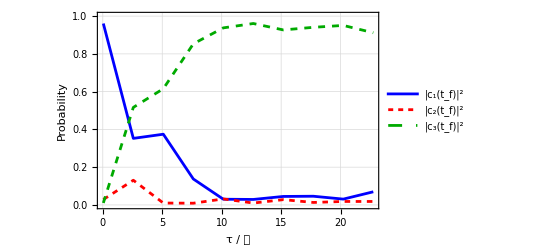

```mathematica
gSa = Show[ListPlot[Transpose[{time,pSa1}], Joined->True,PlotStyle->{Blue}, PlotRange->{0,1},PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_1(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.82}]],ListPlot[Transpose[{time,pSa2}], PlotStyle->{Red, Dashing[0.01]}, PlotRange->All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_2(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.74}]],ListPlot[Transpose[{time,pSa3}], PlotStyle->{Darker[Green], Dashed}, PlotRange-> All,Joined->True,PlotTheme-> "Detailed",FrameLabel ->{"τ / 𝒯", "Probability"},LabelStyle -> {Directive[ 11], FontFamily-> "Arial", Black},PlotLegends->Placed[LineLegend[{Style["|c_3(t_f)|^2",10]},LegendLayout->"Row"],{Right,0.66}]]]
```

## Protocols

6

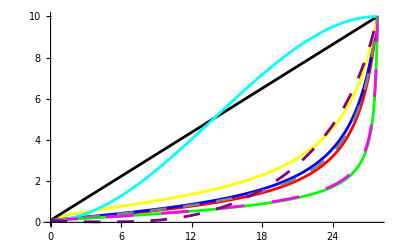

```mathematica
n = 6
Show[Plot[Evaluate[ΩpMA[t]/.Flatten[Part[ProtMA,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Red], Plot[Evaluate[ΩpLA[t]/.Flatten[Part[ProtLA,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Blue],Plot[Evaluate[ΩpFQ[t]/.Flatten[Part[ProtFQ,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Green], 
Plot[Evaluate[ΩpUA[t]/.Flatten[Part[ProtUA,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Yellow], 
Plot[Ωp[t, (n-1)*ΔT + Tmin],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Black], 
Plot[ΩpBCM[t, (n-1)*ΔT + Tmin],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->Cyan], 
Plot[Evaluate[ΩpOP[t]/.Flatten[Part[ProtOP,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->{Magenta, Dashing[0.05]}], 
Plot[Evaluate[ΩpZh[t]/.Flatten[Part[ProtZh,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->{Gray, Dashing[0.03]}],
Plot[Evaluate[ΩpSa[t]/.Flatten[Part[ProtSa,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->{Purple, Dashing[0.03]}]]
```

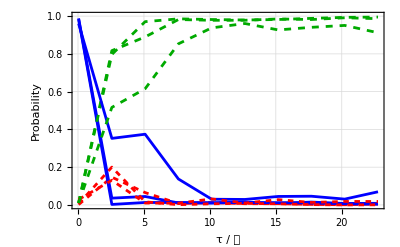

```mathematica
Show[gFQ,gMA, gSa]
```

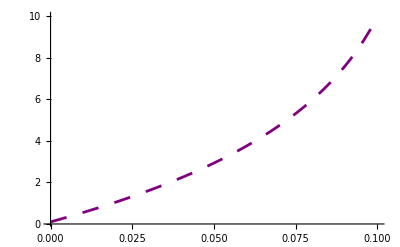
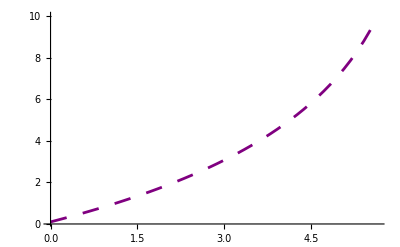
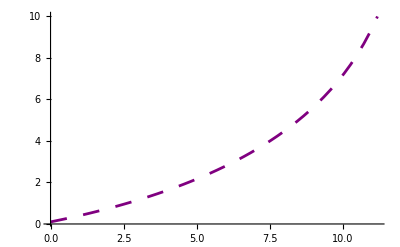
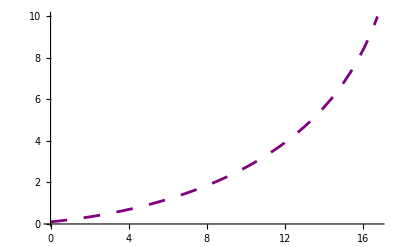
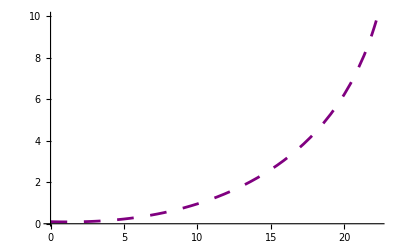
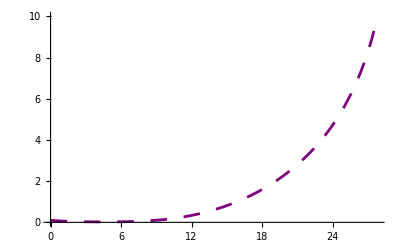
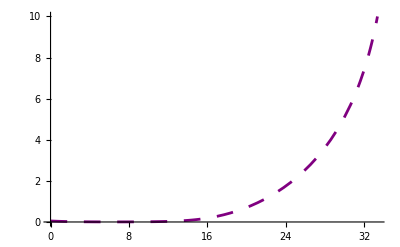
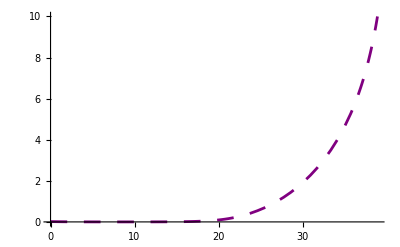

```mathematica
Table[Plot[Evaluate[ΩpSa[t]/.Flatten[Part[ProtSa,n]]],{t,ti,(n-1)*ΔT + Tmin}, PlotRange->All, PlotStyle->{Purple, Dashing[0.03]}],{n,1,m}]
```